```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ant/Sites/JumpStartIM/assets/images/trig

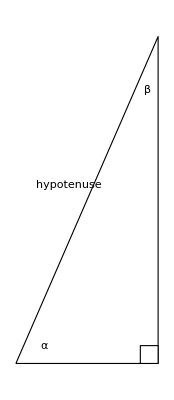

{right-defn-1.pdf,right-defn-1.svg}

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{4,0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Rotate[Text[Style["hypotenuse",Large],{1.5,5}],ArcCos[4/10]]}],
(*Graphics[{Text[Style[4,Large],{2,-0.5}]}],*)
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export[{"right-defn-1.pdf","right-defn-1.svg"},%]
```

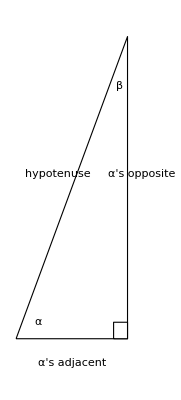

{right-defn-2.pdf,right-defn-2.svg}

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{4,0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Rotate[Text[Style["hypotenuse",Large],{1.5,5}],ArcCos[4/10]]}],
Graphics[{Rotate[Text[Style["α's opposite",Large],{4.5,5}],-Pi/2]}],
Graphics[{Text[Style["α's adjacent",Large],{2,-0.75}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export[{"right-defn-2.pdf","right-defn-2.svg"},%]
```

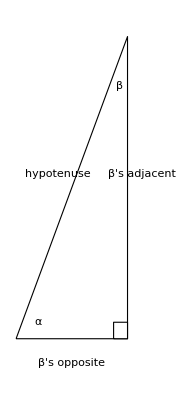

{right-defn-3.pdf,right-defn-3.svg}

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{4,0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Rotate[Text[Style["hypotenuse",Large],{1.5,5}],ArcCos[4/10]]}],
Graphics[{Rotate[Text[Style["β's adjacent",Large],{4.5,5}],-Pi/2]}],
Graphics[{Text[Style["β's opposite",Large],{2,-0.75}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export[{"right-defn-3.pdf","right-defn-3.svg"},%]
```

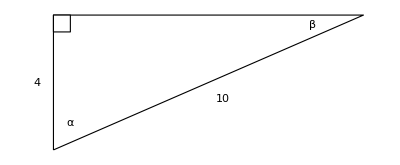

{right-example-1.pdf,right-example-1.svg}

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{0,4},{10 Sin[ArcCos[4/10]],10 Cos[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{0,3.5},{0.5 ,4}]}],
Graphics[{Text[Style[α,Large],{0.5,0.8}]}],
Graphics[{Rotate[Text[Style[10,Large],{5,1.5}],ArcSin[4/10]]}],
Graphics[{Text[Style[4,Large],{-0.5,2}]}],
Graphics[{
Text[Style[β,Large],
{10 Sin[ArcCos[4/10]]-1.5,10 Cos[ArcCos[4/10]]-0.3}]}]
]
Export[{"right-example-1.pdf","right-example-1.svg"},%]
```

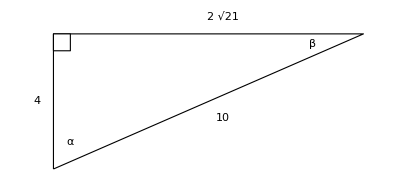

{right-example-2.pdf,right-example-2.svg}

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{0,4},{10 Sin[ArcCos[4/10]],10 Cos[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{0,3.5},{0.5 ,4}]}],
Graphics[{Text[Style[α,Large],{0.5,0.8}]}],
Graphics[{Rotate[Text[Style[10,Large],{5,1.5}],ArcSin[4/10]]}],
Graphics[{Text[Style[4,Large],{-0.5,2}]}],
Graphics[{Text[Style[2Sqrt[21],Large],{5,4.5}]}],
Graphics[{
Text[Style[β,Large],
{10 Sin[ArcCos[4/10]]-1.5,10 Cos[ArcCos[4/10]]-0.3}]}]
]
Export[{"right-example-2.pdf","right-example-2.svg"},%]
```

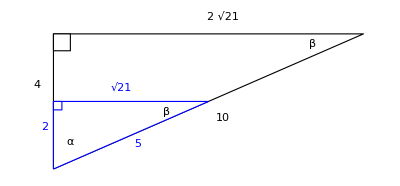

{right-example-3.pdf,right-example-3.svg}

```mathematica
Show[
Graphics[{EdgeForm[{Thick,Dashed}],FaceForm[White],Triangle[{{0,0},{0,4},{10 Sin[ArcCos[4/10]],10 Cos[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[{Thick,Blue}],FaceForm[White],Triangle[{{0,0},{0,2},{5Sin[ArcCos[4/10]],5Cos[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{0,3.5},{0.5 ,4}]}],
Graphics[{EdgeForm[{Thick,Blue}],FaceForm[White],Rectangle[{0,3.5}/2,{0.5 ,4}/2]}],
Graphics[{Text[Style[α,Large],{0.5,0.8}]}],
Graphics[{Rotate[Text[Style[10],{5,1.5}],ArcSin[4/10]]}],
Graphics[{Text[Style[4],{-0.5,2.5}]}],
Graphics[{Text[Style[2Sqrt[21]],{5,4.5}]}],
Graphics[{Rotate[Text[Style[5,Large,Blue],{5,1.5}/2],ArcSin[4/10]]}],
Graphics[{Text[Style[2,Large,Blue],{-0.5,2.5}/2]}],
Graphics[{Text[Style[Sqrt[21],Large,Blue],{4,4.8}/2]}],
Graphics[{
Text[Style[β,Large],
{10 Sin[ArcCos[4/10]]-1.5,10 Cos[ArcCos[4/10]]-0.3}]}],
Graphics[{
Text[Style[β,Large],
{10 Sin[ArcCos[4/10]]-1.5,10 Cos[ArcCos[4/10]]-0.1}/2.3]}]
]
Export[{"right-example-3.pdf","right-example-3.svg"},%]
```

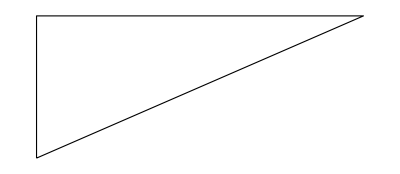

```mathematica
Show[
Graphics[{EdgeForm[{Thick,Black}],FaceForm[White],
Triangle[{{0,0},{3,0}
```